```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

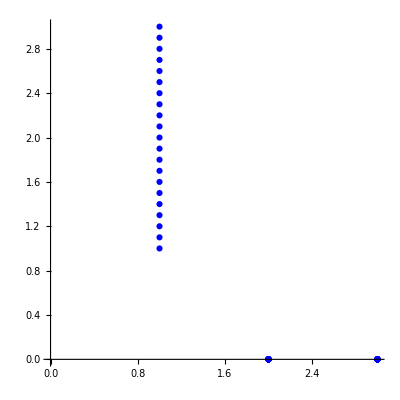

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.repv/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{1.91593,3.,0,0},{1.96799,2.9,0,0},{1.97566,2.8,0,0},{1.9388,2.7,0,0},{1.85803,2.6,0,0},{1.73483,2.5,0,0},{1.57201,2.4,0,0},{1.37418,2.3,0,0},{1.14814,2.2,0,0},{0.902959,2.1,0,0},{0.649512,2.,0,0},{0.399546,1.9,0,0},{0.164436,1.8,0,0},{-0.0459226,1.7,0,0},{-0.223783,1.6,0,0},{-0.363671,1.5,0,0},{-0.462102,1.4,0,0},{-0.517094,1.3,0,0},{-0.527721,1.2,0,0},{-0.493821,1.1,0,0},{-0.415931,1.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0.336557,3.,0,0},{0.136085,2.9,0,0},{-0.0665036,2.8,0,0},{-0.26808,2.7,0,0},{-0.465144,2.6,0,0},{-0.652777,2.5,0,0},{-0.823928,2.4,0,0},{-0.969365,2.3,0,0},{-1.07862,2.2,0,0},{-1.142,2.1,0,0},{-1.15307,2.,0,0},{-1.11065,1.9,0,0},{-1.01917,1.8,0,0},{-0.887304,1.7,0,0},{-0.725484,1.6,0,0},{-0.543629,1.5,0,0},{-0.349729,1.4,0,0},{-0.149521,1.3,0,0},{0.0530264,1.2,0,0},{0.254769,1.1,0,0},{0.452265,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv